Strings and Text

Another thing the Wolfram Language lets you compute with is text. You enter text as a string, indicated by quotes (").

Enter a string:

```mathematica
"This is a string."
```

This is a string.

Just like when you enter a number, a string on its own comes back unchanged—except that the quotes aren’t visible when the string is displayed. There are many functions that work on strings. Like StringLength, which gives the length of a string.

StringLength counts the number of characters in a string:

```mathematica
StringLength["hello"]
```

5

StringReverse reverses the characters in a string:

```mathematica
StringReverse["hello"]
```

olleh

ToUpperCase makes all the characters in a string uppercase (capital letters):

```mathematica
ToUpperCase["I'm writing in the Wolfram Language!"]
```

I'M WRITING IN THE WOLFRAM LANGUAGE!

StringTake takes a certain number of characters from the beginning of a string:

```mathematica
StringTake["this is about strings",10]
```

this is ab

If you take 10 characters, you get a string of length 10:

```mathematica
StringLength[StringTake["this is about strings",10]]
```

10

StringJoin joins strings (don’t forget spaces if you want to separate words):

```mathematica
StringJoin["Hello"," ", "there!", " How are you?"]
```

Hello there! How are you?

You can make lists of strings, then apply functions to them.

A list of strings:

```mathematica
{"apple","banana","strawberry"}
```

{apple,banana,strawberry}

Get the first two characters from each string:

```mathematica
StringTake[{"apple","banana","strawberry"},2]
```

{ap,ba,st}

StringJoin joins the strings in a list:

```mathematica
StringJoin[{"apple","banana","strawberry"}]
```

applebananastrawberry

Sometimes it’s useful to turn strings into lists of their constituent characters. Each character is actually a string itself, of length 1.

Characters breaks a string into a list of its characters:

```mathematica
Characters["a string is made of characters"]
```

{a, ,s,t,r,i,n,g, ,i,s, ,m,a,d,e, ,o,f, ,c,h,a,r,a,c,t,e,r,s}

Once you’ve broken a string into a list of characters, you can use all the usual list functions on it.

Sort the characters in a string:

```mathematica
Sort[Characters["a string of characters"]]
```

{ , , ,a,a,a,c,c,e,f,g,h,i,n,o,r,r,r,s,s,t,t}

The invisible elements at the beginning of the list are space characters. If you want to see strings in the form you’d input them, complete with "...", use InputForm.

InputForm shows strings as you would input them, including quotes:

```mathematica
InputForm[Sort[Characters["a string of characters"]]]
```

{" ", " ", " ", "a", "a", "a", "c", "c", "e", "f", "g", "h", "i", "n", "o", "r", 
 "r", "r", "s", "s", "t", "t"}

Functions like StringJoin and Characters work on strings of any kind; it doesn’t matter if they’re meaningful text or not. There are other functions, like TextWords, that specifically work on meaningful text, written, say, in English.

TextWords gives a list of the words in a string of text:

```mathematica
TextWords["This is a sentence. Sentences are made of words."]
```

{This,is,a,sentence,Sentences,are,made,of,words}

This gives the length of each word:

```mathematica
StringLength[TextWords["This is a sentence. Sentences are made of words."]]
```

{4,2,1,8,9,3,4,2,5}

TextSentences breaks a text string into a list of sentences:

```mathematica
TextSentences["This is a sentence. Sentences are made of words."]
```

{This is a sentence.,Sentences are made of words.}

There are lots of ways to get text into the Wolfram Language. One example is the WikipediaData function, which gets the current text of Wikipedia articles.

Get the first 100 characters of the Wikipedia article about “computers”:

```mathematica
StringTake[WikipediaData["computers"],100]
```

A computer is a general-purpose device that can be programmed to carry out a set of arithmetic or lo

A convenient way to get a sense of what’s in a piece of text is to create a word cloud. The function WordCloud does this.

Create a word cloud for the Wikipedia article on “computers”:

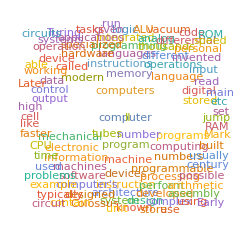

```mathematica
WordCloud[WikipediaData["computers"]]
```

Not surprisingly, “computer” and “computers” are the most common words in the article.

The Wolfram Language has lots of built-in knowledge about words that appear in English and other languages. WordList gives lists of words.

Get the first 20 words from a list of common English words:

```mathematica
Take[WordList[ ],20]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess}

Make a word cloud from the first letters of all the words:

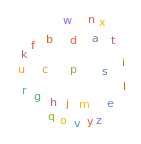

```mathematica
WordCloud[StringTake[WordList[ ],1]]
```

Strings don’t have to contain text. In a juxtaposition of ancient and modern, we can for example generate Roman numerals as strings.

Generate the Roman numeral string for 1988:

```mathematica
RomanNumeral[1988]
```

MCMLXXXVIII

Make a table of the Roman numerals for numbers up to 20:

```mathematica
Table[RomanNumeral[n],{n,20}]
```

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX}

As with everything, we can do computations on these strings. For example, we can plot the lengths of successive Roman numerals.

Plot the lengths of the Roman numerals for numbers up to 100:

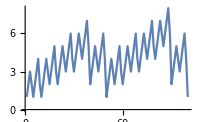

```mathematica
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}]]
```

IntegerName gives the English name of an integer.

Generate a string giving the name of the integer 56:

```mathematica
IntegerName[56]
```

fifty-six

Here’s a plot of the lengths of integer names in English:

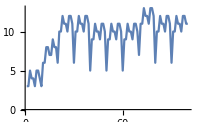

```mathematica
ListLinePlot[Table[StringLength[IntegerName[n]],{n,100}]]
```

There are various ways to turn letters into numbers (and vice versa).

Alphabet gives the alphabet:

```mathematica
Alphabet[ ]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

LetterNumber tells you where in the alphabet a letter appears:

```mathematica
LetterNumber[{"a","b","x","y","z"}]
```

{1,2,24,25,26}

FromLetterNumber does the opposite:

```mathematica
FromLetterNumber[{10,11,12,13,14,15}]
```

{j,k,l,m,n,o}

Alphabet knows about non-English alphabets too:

```mathematica
Alphabet["Russian"]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

```mathematica
Transliterate[Alphabet["Russian"]]
```

{a,b,v,g,d,e,e,z,z,i,j,k,l,m,n,o,p,r,s,t,u,f,h,c,c,s,s,ʺ,y,ʹ,e,u,a}

This transliterates the word “wolfram” into the Russian alphabet:

```mathematica
Transliterate["wolfram","Russian"]
```

уолфрам

The characters in strings can be anything you can type on your computer, including for example emoji.

Reverse the characters in a string made of emoji:

```mathematica
StringReverse["🐺😖😕😌😀😃😁🐏"]
```

🐏😁😃😀😌😕😖🐺

If you want to, you can also turn text into images, which you can then manipulate using image processing. The function Rasterize makes a raster, or bitmap, of something.

Generate an image of a piece of text:

```mathematica
Rasterize[Style["ABC🐱",80]]
```

-Graphics-

Do image processing on it:

```mathematica
EdgeDetect[Rasterize[Style["ABC🐱",80]]]
```

-Graphics-

Vocabulary

"string" |   | a string 
StringLength["string"] |   | length of a string 
StringReverse["string"] |   | reverse a string 
StringTake["string",4] |   | take characters at the beginning of a string 
StringJoin["string","string"] |   | join strings together 
StringJoin[{"string","string"}] |   | join a list of strings 
ToUpperCase["string"] |   | convert characters to uppercase 
Characters["string"] |   | convert a string to a list of characters 
TextWords["string"] |   | list of words from a string 
TextSentences["string"] |   | list of sentences 
WikipediaData["topic"] |   | Wikipedia article about a topic 
WordCloud["text"] |   | word cloud based on word frequencies 
WordList[ ] |   | list of common words in English 
Alphabet[ ] |   | list of letters of the alphabet 
LetterNumber["c"] |   | where a letter appears in the alphabet 
FromLetterNumber[n] |   | letter appearing at a position in the alphabet 
Transliterate["text"] |   | transliterate text in any language into English
Transliterate["text","alphabet"] |   | transliterate text into other alphabets
RomanNumeral[n] |   | convert a number to its Roman numeral string 
IntegerName[n] |   | convert a number to its English name string
InputForm["string"] |   | show a string with quotes 
Rasterize["string"] |   | make a bitmap image

"31 Exercises Available"
"with 13 extras" | "Get Started »"

Join two copies of the string "Hello". »

| Expected output: |  
  | "HelloHello" |

Make a single string of the whole alphabet, in uppercase. »

| Expected output: |  
  | "ABCDEFGHIJKLMNOPQRSTUVWXYZ" |

Generate a string of the alphabet in reverse order. »

| Expected output: |  
  | "zyxwvutsrqponmlkjihgfedcba" |

Join 100 copies of the string "AGCT". »

| Expected output: |  
  | "AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT" |

Use StringTake, StringJoin and Alphabet to get "abcdef". »

| Expected output: |  
  | "abcdef" |

Create a column with increasing numbers of letters from the string "this is about strings". »

| Expected output: |  
  | "t"
"th"
"thi"
"this"
"this "
"this i"
"this is"
"this is "
"this is a"
"this is ab"
"this is abo"
"this is abou"
"this is about"
"this is about "
"this is about s"
"this is about st"
"this is about str"
"this is about stri"
"this is about strin"
"this is about string"
"this is about strings" |

Make a bar chart of the lengths of the words in “A long time ago, in a galaxy far, far away”. »

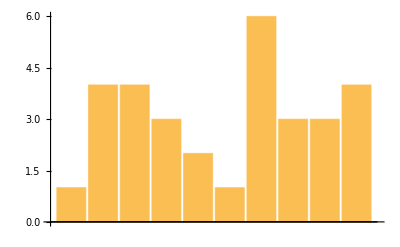
| Expected output: |  
  | -Graphics- |

Find the string length of the Wikipedia article for “computer”. »

| Sample expected output: |  
  | 58109 |

Find how many words are in the Wikipedia article for “computer”. »

| Sample expected output: |  
  | 8960 |

Find the first sentence in the Wikipedia article about “strings”. »

| Sample expected output: |  
  | "String or strings may refer to:" |

Make a string from the first letters of all sentences in the Wikipedia article about computers. »

| Sample expected output: |  
  | "AMTATASCESEMTTTCTPP=ATTDBTTT==DTLTTTITIIMTTAAATTTIASIBIAITITIITS=CCATFTTTAEBNH=DHTTTTAB==BTDETTITIRTZT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAAGTBAIT=TJFCJTHATHTTIWITT=TTDTKIHKNNHPNIMTGFTWISTIS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCIW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETBOBSA=CTITTITCIIA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M" |

Find the maximum word length among English words from WordList[ ]. »

| Sample expected output: |  
  | 23 |

Count the number of words in WordList[ ] that start with “q”. »

| Sample expected output: |  
  | 197 |

Make a line plot of the lengths of the first 1000 words from WordList[ ]. »

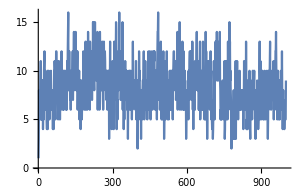
| Sample expected output: |  
  | -Graphics- |

Use StringJoin and Characters to make a word cloud of all letters in the words from WordList[ ]. »

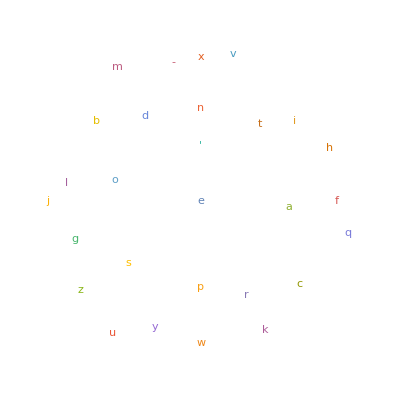
| Sample expected output: |  
  | -Graphics- |

Use StringReverse to make a word cloud of the last letters in the words from WordList[ ]. »

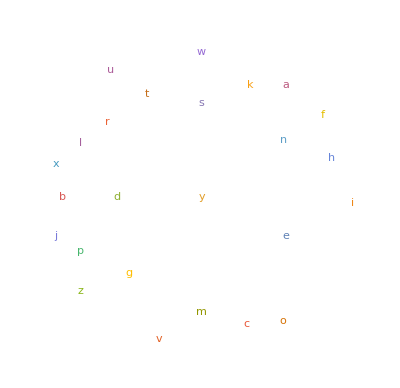
| Sample expected output: |  
  | -Graphics- |

Find the Roman numerals for the year 1959. »

| Expected output: |  
  | "MCMLIX" |

Find the maximum string length of any Roman-numeral year from 1 to 2020. »

| Expected output: |  
  | 13 |

Make a word cloud from the first characters of the Roman numerals up to 100. »

| Expected output: |  
  |  |

Use Length to find the length of the Russian alphabet. »

| Expected output: |  
  | 33 |

Generate the uppercase Greek alphabet. »

| Expected output: |  
  | {"Α","Β","Γ","Δ","Ε","Ζ","Η","Θ","Ι","Κ","Λ","Μ","Ν","Ξ","Ο","Π","Ρ","Σ","Τ","Υ","Φ","Χ","Ψ","Ω"} |

Make a bar chart of the letter numbers in “wolfram”. »

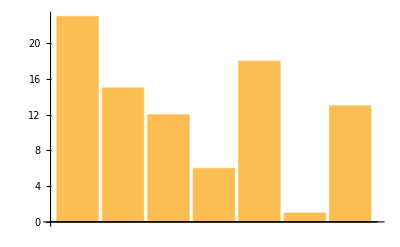
| Expected output: |  
  | -Graphics- |

Use FromLetterNumber to make a string of 1000 random letters. »

| Sample expected output: |  
  | "chfpmqpcyncvrvvsczeyfihbbtyvwtejczkwdpfxwtfncqphiptelkyrkectbxxccksjxzubmcfsdveiexjzvldmyduewyayvstpajkttgelnayfsnlrnvmvhoomknurnjobsexzxiajjwdewgxldwjnwgqtmuwqalzopswwbvbrcdkaczpvpekkbcwotsevhukcbzjrbgtheypludcajvdcukftzsctsctvuimujiyrbgkaeuuiavggepzipouyhyvqlyjvbewluhqfgvmwwqtzjwmeoyjsbinlvmzpbjrdlelyrfzpwfjfhlowquqawzrbufvilscljlptgilvzggomjtlbtbvttwcqrucmsydwmbxqedqewjdfsevrzybymhwalzbaqazkhsrbfsalmtkxbcyxliaapasvdqvtqptoudinbabftutdoijvlmlgnodeiyprjkmfsdhdqmagbohksoyevwpljdmdglibgtrfbplfsewhrnoqnkryhaazlfqlikxmrwamtfdwiqyalivbqgrocsiavczjgtidffntqavtjtpwyjpbynwmmxfhnkzynrcvmewbtdsoanygujfooupnozbaetulhrpbngnxojqnbtsmtfelnrqsydvlxlxtcgfltegagyobeonakngwjchqgpycjdzaotfvxigouzmogrdpwwkkttsieddsmahqthvymvkcjlzigwenxvekurkixqjrormukhqyyzygvzntzptuooboriyjkaxofuediewvxrrifcdjfrlqeuneyrwppapdpooitwcevydjozxxfwlnzwulzjacoiryqogroikztsbbwbkfcjqvjlvdwabuiwoehnqbuxodlwnqidwbtzpbkdfwmjgtczbqbgldivjjprzuslsoszcghcklobxeknddhkgjvvhtsuffdrfhefjhawtxylpfxzjumgbcdhetsankemseloadcegkizwddlsqwzuxbpz" |

Make a list of 100 random 5-letter strings. »

| Sample expected output: |  
  | {"vjdxl","yeftc","tguag","rsdyz","jvbgm","pdntg","wqupa","xznnh","gmuvl","nzxqd","qnokn","tyues","ukblh","mdats","pbjuu","hjifa","xnbtw","xquds","egttt","fkkax","udcrc","aucim","lulzv","isjpn","umgax","kdhoy","nysyq","ukhwl","remdz","ljjzn","ujtti","bircn","hnaqd","jhfwg","jlyju","jcegb","gcnso","rryks","hbnhg","gvoko","pcwjk","lnhps","umjom","knfia","gpxvw","esvzo","euiam","vxlnl","yajli","twfiz","veong","htndw","fggfy","jkvou","yurvh","buesn","svgzn","paevj","bmrza","hbiqc","cjazs","kkiuw","wtzrl","lqcpm","pwnng","xepji","wmmcl","fhlfe","thakf","nckgv","fzttu","hdffz","uadni","asfav","wouah","rtzaz","kjfhi","jaaiu","uinzk","bcarm","zujeq","icoko","ccaxw","eynlq","gnlso","jpkiu","wsrhb","bjlvz","ahdmc","nqpot","netkc","cxnzv","lyfky","uebwg","lklqj","iwvlp","ayxfv","rxjge","mheur","gxzmo"} |

Transliterate “wolfram” into Greek. »

| Expected output: |  
  | "βολφραμ" |

Make a string of 10 wolf, ram emoji 🐺🐏🐺🐏.... »

| Expected output: |  
  | "🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏🐺🐏" |

Get the Arabic alphabet and transliterate it into English. »

| Expected output: |  
  | {"a","b","t","th","j","h","kh","d","dh","r","z","s","sh","s","d","t","z","ʿ","gh","f","q","k","l","m","n","h","w","y"} |

Make a white-on-black size-200 letter “A”. »

| Expected output: |  
  | -Graphics- |

Use Manipulate to make an interactive selector of size-100 characters from the alphabet, controlled by a slider. »

| Expected output: |  
  |  |

Use Manipulate to make an interactive selector of black-on-white outlines of rasterized size-100 characters from the alphabet, controlled by a menu. »

| Expected output: |  
  |  |

Use Manipulate to create a “vision simulator” that blurs a size-200 letter “A” by an amount from 0 to 50. »

| Expected output: |  
  |  |

Generate a string of the alphabet followed by the alphabet written in reverse. »

| Expected output: |  
  | "abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba" |

Make a column of a string of the alphabet and its reverse. »

| Expected output: |  
  | "abcdefghijklmnopqrstuvwxyz"
"zyxwvutsrqponmlkjihgfedcba" |

Find how many sentences are in the Wikipedia article for “computer”. »

| Expected output: |  
  | 452 |

Join together without spaces, etc. the words in the first sentence in the Wikipedia article for “strings”. »

| Expected output: |  
  | "Stringorstringsmayreferto" |

Find the length of the longest word in the Wikipedia article about computers. »

| Expected output: |  
  | 25 |

Plot the lengths of Roman numerals for numbers up to 2000. »

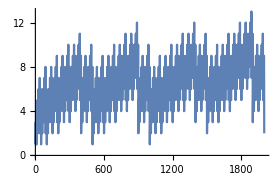
| Expected output: |  
  | -Graphics- |

Generate a string by joining the Roman numerals up to 100. »

| Expected output: |  
  | "IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC" |

Make a line plot of the successive letter numbers for the concatenation of all Roman numerals up to 30. »

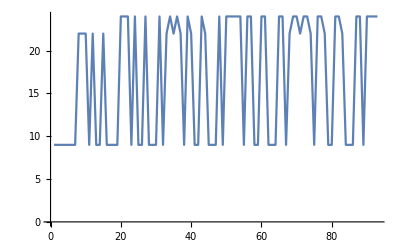
| Expected output: |  
  | -Graphics- |

Find the maximum string length of the name of any integer up to 1000. »

| Expected output: |  
  | 27 |

Make a list of uppercase size-20 letters of the alphabet in random colors. »

| Expected output: |  
  | {"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z"} |

Make a list of 100 random 5-letter strings with the Russian alphabet. »

| Expected output: |  
  | {"щёярф","цруйл","пхёкц","вгхфв","флэшм","яёуйу","лчтло","гнхшу","клчщч","эйарэ","совэф","цхшни","кдпфз","здъжь","ыйряп","змгщд","яфтбм","каоеэ","лкжрб","уатоо","нзквк","сонль","юфщзс","ябгшш","нясзо","хоэсв","псикх","днэхх","ъбшнщ","вюадг","ъчизб","цпвюа","ныиья","пгбби","ыхжзй","хвзет","чивир","чзгвм","млчюн","шгшнж","снслж","жйзьа","вйрак","вжънх","иёжщи","кшъиф","йцюую","цизшз","юшеях","хещэб","ффвмв","юяяко","лчвля","фцаьс","чрхиь","пунзщ","резуя","мпущд","гызшг","кёжмэ","бзяёя","хдхдъ","юзфща","ызуцр","ьяящл","оэмщи","эгщов","уфпвл","ядьщэ","йуэёэ","цснск","йпцжъ","йгухл","урмщр","щгхоф","ащвфх","кчьаь","улчпу","асмлж","какхй","рврвг","олйзя","ёцшцэ","энсав","еёяуб","чцеяс","вшэеи","чомры","ипбьэ","ьяфым","шидяб","щаюкы","шобро","айэнй","ашфгк","съгрм","ыфафщ","пбянс","фмсгф","хрубё"} |

Create a Manipulate to display edges in a size-200 letter “A”, blurred from 0 to 50. »

| Expected output: |  
  |  |

Add together white-on-black size-200 letters A and B. »

| Expected output: |  
  | -Graphics- |

Q&A

What is the difference between "x" and x?

"x" is a string; x is a Wolfram Language symbol, just like Plus or Max, that can be defined to actually do computations. We’ll talk much more about symbols later.

How do I enter characters that aren’t on my keyboard?

You can use whatever methods your computer provides, or you can do it directly with the Wolfram Language using constructs such as \[Alpha].

How do I put quotes (") inside a string?

Use \" (and if you want to put \" literally in the string, use \\\"). (You’ll use a lot of backslashes if you want to put \\\" in: \\\\\\\".)

How are the colors of elements in word clouds determined?

By default it’s random within a certain color palette. You can specify it if you want to.

How come the word cloud shows “s” as the most common letter?

Because it is the most common first letter for common words in English. If you look at all letters, the most common is “e”.

What about letters that aren’t English? How are they numbered?

LetterNumber["α","Greek"] gives numbering in the Greek alphabet. All characters are assigned a character code. You can find it using ToCharacterCode.

What alphabets does the Wolfram Language know about?

Basically all the ones that are used today. Try “Greek” or “Arabic”, or the name of a language. Note that when a language uses accented characters, it’s sometimes tricky to decide what’s “in” the alphabet, and what’s just derived from it.

Can I translate words instead of just transliterating their letters?

Yes. Use WordTranslation. See Section 35.

Can I get lists of common words in languages other than English?

Yes. Use WordList[Language→"Spanish"], etc.

Tech Notes

RandomWord[10] gives 10 random words. How many of them do you know?

StringTake["string",-2] takes 2 characters from the end of the string.

Every character, whether “a”, “α”, “狼” or “🐼”, is represented by a Unicode character code, found with ToCharacterCode. You can explore “Unicode space” with FromCharacterCode.

Characters can look very different when they’re shown in different fonts; emoji can look very different between different operating systems.

If you get a different result from WikipediaData, that’s because Wikipedia has been changed.

WordCloud automatically removes “uninteresting” words in text, like “the”, “and”, etc.

If you can’t figure out the name of an alphabet or language, use ctrl= (as described in Section 16) to give it in natural language form.

More to Explore

Guide to String Manipulation in the Wolfram Language »